## Functions

```mathematica
H[θ_]  :=H[θ]= θ/(1+θ)
Ho[θ_,ρ_]:=Ho[θ,ρ]= (18 + 13 ρ + ρ^2 + 36θ + 22θ^2 + 4θ^3 +  ρ(6θ + θ^2))/((1+θ)(18 + 13ρ+ρ^2 + 54θ + 40θ^2 + 8θ^3 + ρ(ρ θ + 19θ + 6θ^2)))
H2[θ_,ρ_] :=H2[θ,ρ]= (θ^2(36 + 14ρ + ρ^2 + 36θ + 6ρ θ + 8θ^2))/((1+θ)(18 + 13ρ+ρ^2 + 54θ + 40θ^2 + 8θ^3 + ρ(ρ θ + 19θ + 6θ^2)))
H1[θ_,ρ_] :=H1[θ,ρ]= 1- Ho[θ,ρ] - H2[θ,ρ]

re[d_, g_, rbp_, L_] := rbp(d + 2(g/rbp)L(1 - ⅇ^(-d/L)))
H[θ_]  := θ/(1+θ)

Ho[θ_,d_, g_, rbp_, L_]:= (18 + 13 re[d, g, rbp, L] + re[d, g, rbp, L]^2 + 36θ + 22θ^2 + 4θ^3 +  re[d, g, rbp, L](6θ + θ^2))/((1+θ)(18 + 13re[d, g, rbp, L]+re[d, g, rbp, L]^2 + 54θ + 40θ^2 + 8θ^3 + re[d, g, rbp, L](re[d, g, rbp, L]θ + 19θ + 6θ^2)))

H2[θ_,d_, g_, rbp_, L_] := (θ^2(36 + 14re[d, g, rbp, L] + re[d, g, rbp, L]^2 + 36θ + 6re[d, g, rbp, L] θ + 8θ^2))/((1+θ)(18 + 13re[d, g, rbp, L]+re[d, g, rbp, L]^2 + 54θ + 40θ^2 + 8θ^3 + re[d, g, rbp, L](re[d, g, rbp, L] θ + 19θ + 6θ^2)))

H1[θ_,d_, g_, rbp_, L_] := 1- Ho[θ,re[d, g, rbp, L]] - H2[θ,re[d, g, rbp, L]]
```

```mathematica
(*Expectations replacing rho with re*)
```

```mathematica
(*note pooling individuals for a single individual just formats the data from the 'dataset' for the functions below calculating likelihoods*)
PoolIndividuals[chr_]:=Module[{chrUnbinned},
chrUnbinned = chr[[All,3;;]];
chrUnbinned = {#[[1]][[1]],Total[#[[All,2]]],Total[#[[All,3]]],Total[#[[All,4]]],Mean[#[[All,-1]]]}&/@(Values@GroupBy[chrUnbinned[[All,All]],First]);
chrUnbinned
];
BinnedChrCounts[chrUnbinned_,binSize_]:=Module[{interval = binSize, binned1,binned2},
binned1 = Table[{ #[[1]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]],#[[2]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]],#[[3]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]],#[[4]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]]},{i,1,Floor@(Length[chrUnbinned]/interval)}];
binned1= SortBy[binned1,First];
binned2= {Mean[#[[1]]],Total[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&/@binned1;
binned2
]
BinnedChrProp[chrUnbinned_,binSize_]:=Module[{interval = binSize, binned1,binned2},
binned1 = Table[{ #[[1]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]],#[[2]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]],#[[3]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]],#[[4]]&/@chrUnbinned[[interval(i-1)+1;;interval(i)]]},{i,1,Floor@(Length[chrUnbinned]/interval)}];
binned1= SortBy[binned1,First];
binned2= {Mean[#[[1]]],Total[#[[2]]],Total[#[[3]]],Total[#[[4]]]}&/@binned1;
binned2 = {#[[1]], #[[2]] /Total[#[[2;;4]]],#[[3]]/Total[#[[2;;4]]],#[[4]]/Total[#[[2;;4]]]}&/@binned2;
binned2
]
GetChrLikeFun[binnedChr_]:=Module[{binned2 = binnedChr,binnedLike},
binnedLike=Sum[ binned2[[i,2]]*Log[ Ho[θ, binned2[[i,1]], g, rbp, L] ] +binned2[[i,3]] Log[H1[θ,  binned2[[i,1]], g, rbp, L]] +binned2[[i,4]] Log[H2[θ, binned2[[i,1]], g, rbp, L] ],{i,1,Length[binned2]}];
binnedLike
];
CalculateLikeCounts[unbinnedChr_,binSize_]:=Module[
{binnedCounts = GetChrLikeFun[BinnedChrCounts[ unbinnedChr,binSize]],
countEstimate,,propEstimate
},
countEstimate = NMaximize[{binnedCounts
,0.0001<θ<0.1,25≤L≤500, 0.0000000001 < rbp < 0.1  , 0.0000001 < g  < 0.1},{θ,rbp,g,L},MaxIterations->2000,PrecisionGoal->10];
countEstimate
];
CalculateLikeCountsAndPropsBinned[unbinnedChr_,binSize_]:=Module[
{binnedCounts = GetChrLikeFun[BinnedChrCounts[ unbinnedChr,binSize]],
binnedProp = GetChrLikeFun[BinnedChrProp[unbinnedChr,binSize]],
countEstimate,,propEstimate
},
countEstimate = NMaximize[{binnedCounts
,0.0001<θ<0.1,25≤L≤500, 0.0000000001 < rbp < 0.1  , 0.0000001 < g  < 0.1},{θ,rbp,g,L},MaxIterations->2000,PrecisionGoal->10];
propEstimate = NMaximize[{binnedProp
,0.0001<θ<0.1,25≤L≤500, 0.0000000001 < rbp < 0.1  , 0.0000001< g  < 0.1},{θ,rbp,g,L},MaxIterations->2000,PrecisionGoal->10];
{countEstimate,propEstimate}
];
```

## Data:

```mathematica
PoolIndividuals[chr_]:=Module[{chrUnbinned},
chrUnbinned = chr[[All,3;;]];
chrUnbinned = {#[[1]][[1]],Total[#[[All,2]]],Total[#[[All,3]]],Total[#[[All,4]]],Mean[#[[All,-1]]]}&/@(Values@GroupBy[chrUnbinned[[All,All]],First]);
chrUnbinned
];

GetChrLikeFun[binnedChr_]:=Module[{binned2 = binnedChr,binnedLike},
binnedLike=Sum[ binned2[[i,2]]*Log[ Ho[binned2⟦i,5⟧, binned2[[i,1]], g, rbp, L] ] +binned2[[i,3]] Log[H1[binned2⟦i,5⟧,  binned2[[i,1]], g, rbp, L]] +binned2[[i,4]] Log[H2[binned2⟦i,5⟧, binned2[[i,1]], g, rbp, L] ],{i,1,Length[binned2]}];
binnedLike
];
```

```mathematica
data=Import["~/Dropbox/projects/gene_conversion/mathematicaInputMice_unbinned.tsv" ,"Dataset", "HeaderLines" -> 1];
fullDataCountsByDistance = PoolIndividuals[data[Select[#chrom ≠ "chrX"&]]];
```

```mathematica
estimatesChr19MinDist100Python = {0.002673853733400405,0.004444332823674365,113.24025414204982} (* kappa, gamma, L*) (*here, distance is actually 101, not 100, but should make little difference*)
```

{0.00267385,0.00444433,113.24}

```mathematica
chr19 = PoolIndividuals[data[Select[#chrom == "chr19"&]]];
chr19MinDist100 = chr19⟦100;;All⟧;
```

```mathematica
likeFunChr19 = GetChrLikeFun[chr19MinDist100]
```

239345024 Log[(0.992294 (18.2809+13.0467 (1000+(2 (1-ⅇ^(-1000/L)) g L)/rbp) rbp+(1000+(2 (1-ⅇ^(-1000/L)) g L)/rbp)^2 rbp^2))/(18.4218+13 (1000+(2 (1-ⅇ^(-1000/L)) g L)/rbp) rbp+(1000+(2 (1-ⅇ^(-1000/L)) g L)/rbp)^2 rbp^2+(1000+(2 (1-ⅇ^(-1000/L)) g L)/rbp) rbp (0.147906+0.00776547 (1000+(2 (1-ⅇ^(-1000/L)) g L)/rbp) rbp))]+18848 Log[(0.0000598379 (1))/(18.4218+1+1+1)]+2699+4233508 Log[1]+4234223 Log[1-(0.992343 (18.2791+13.0464 (100+(2 (1-ⅇ^1) g L)/rbp) rbp+(100+(2 (1-1)11 L)/rbp)^2 rbp^2))/(18.4191+13 (100+(2 (1-1) g L)/rbp) rbp+(100+1)^2 rbp^2+(100+(2 (1-ⅇ^(-100/L)) g L)/rbp) rbp (0.146967+0.0077163 (100+(2 (1-ⅇ^1) g L)/rbp) rbp))-(0.0000590853 (36.2783+14.0463 (100+(2 (1-ⅇ^(-100/L)) g L)/rbp) rbp+(100+(2 (1-ⅇ^1) g L)/rbp)^2 rbp^2))/(18.4191+13 (100+(2 (1-ⅇ^(-100/L)) g L)/rbp) rbp+(100+(2 (1-ⅇ^1) g L)/rbp)^2 rbp^2+(100+(2 (1-ⅇ^(-100/L)) g L)/rbp) rbp (0.146967+0.0077163 (100+(2 (1-ⅇ^(-100/L)) g L)/rbp) rbp))]
 |  |  |  |

#### gc by L like surface

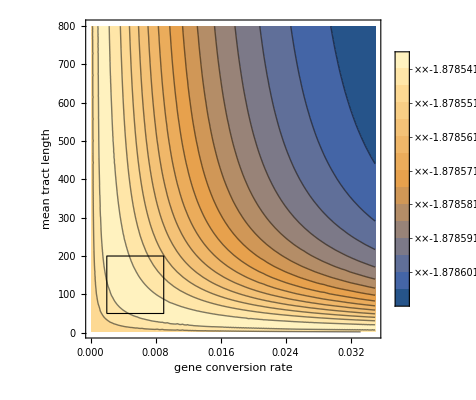

```mathematica
pGcByLBig = Show[
ContourPlot[
Evaluate[likeFunChr19/.{rbp->0.002673853733400405}],
{g,0.0001,.035},{L,2,800},
ColorFunctionScaling->True,
PlotLegends->Automatic,
Contours->{Automatic,20},
ContourStyle->Thick,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"gene conversion rate","mean tract length"},
ImageSize->Automatic,PlotRangePadding->Automatic,
Epilog->{
Inset[Graphics[{Black,Text[Style["+",14,Bold]]}],{0.004444332823674365,113.24025414204982}]}
],
Graphics[{EdgeForm[{Thick,Dotted,Black}],FaceForm[],Rectangle[{0.002,50},{0.009,200}]}]
]
```

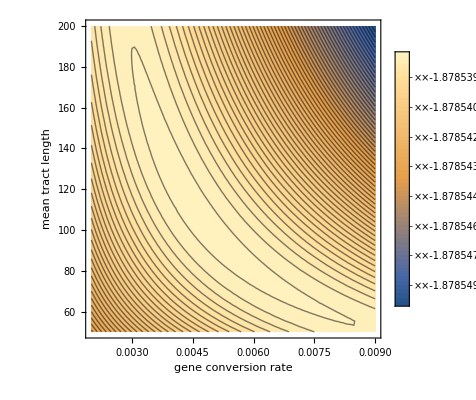

```mathematica
pGCByLSmall = Show[
ContourPlot[
Evaluate[likeFunChr19/.{rbp->0.002673853733400405}],
{g,0.002,0.009},{L,50,200},
ColorFunctionScaling->True,
PlotLegends->Automatic,
Contours->{Automatic,60},
ContourStyle->Thick,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"gene conversion rate","mean tract length"},
ImageSize->Automatic,PlotRangePadding->Automatic,
Epilog->{
Inset[Graphics[{Black,Text[Style["+",14,Bold]]}],{0.004444332823674365,113.24025414204982}]}
]
(*,Graphics[{EdgeForm[{Thick,Dotted,Black}],FaceForm[],Rectangle[{0.0018,140},{0.003,280}]}]*)
]
```

#### XO by GC like surface

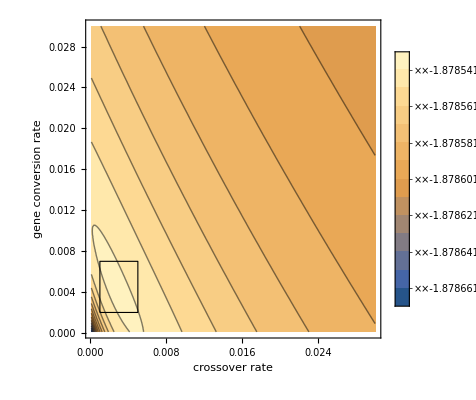

```mathematica
pXoByGcBig=Show[
ContourPlot[
Evaluate[likeFunChr19/.{L->113.24}],
{rbp,0.0001,0.03},{g,0.0001,0.03},
ColorFunctionScaling->True,
PlotLegends->Automatic,
Contours->{Automatic,20},
ContourStyle->Thick,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"crossover rate","gene conversion rate"},
ImageSize->Automatic,PlotRangePadding->Automatic,
Epilog->Inset[Graphics[{Black,Text[Style["+",14,Bold]]}],{0.00267385,0.00444433}]
],
Graphics[{EdgeForm[{Thick,Dotted,Black}],FaceForm[],Rectangle[{.001,0.002},{0.005,0.007}]}]
]
```

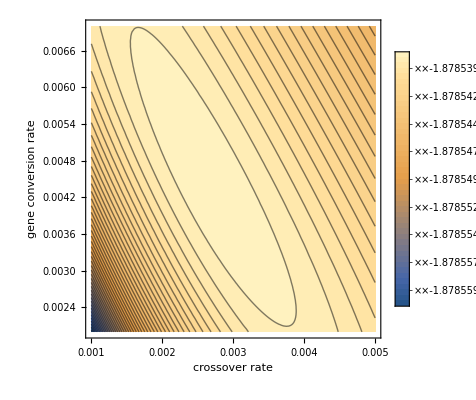

```mathematica
pXoByGcSmall=Show[
ContourPlot[
Evaluate[likeFunChr19/.{L->113.24}],
{rbp,0.001,0.005},{g,0.002,0.007},
ColorFunctionScaling->True,
PlotLegends->Automatic,
Contours->{Automatic,60},
ContourStyle->Thick,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"crossover rate","gene conversion rate"},
ImageSize->Automatic,PlotRangePadding->Automatic,
Epilog->Inset[Graphics[{Black,Text[Style["+",14,Bold]]}],{0.00267385,0.00444433}]
]
]
```

#### xo rate vs tract length

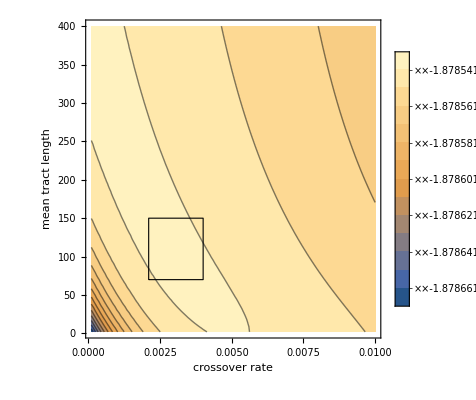

```mathematica
pXoByLBig=Show[
ContourPlot[
Evaluate[likeFunChr19/.{g->0.00444433}],
{rbp,0.0001,.01},{L,2,400},
ColorFunctionScaling->True,
PlotLegends->Automatic,
Contours->{Automatic,20},
ContourStyle->Thick,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"crossover rate","mean tract length"},
ImageSize->Automatic,PlotRangePadding->Automatic,
Epilog->{
Inset[Graphics[{Black,Text[Style["+",14,Bold]]}],{0.002673853733400405,113.24025414204982}]}
],
Graphics[{EdgeForm[{Thick,Dotted,Black}],FaceForm[],Rectangle[{0.0021,70},{0.004,150}]}]
]
```

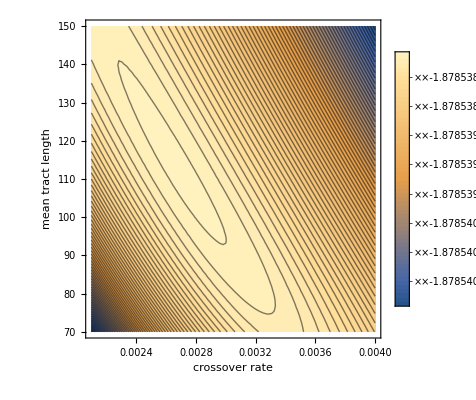

```mathematica
pXoByLSmall=Show[
ContourPlot[
Evaluate[likeFunChr19/.{g->0.00444433}],
{rbp,0.0021,0.004},{L,70,150},
ColorFunctionScaling->True,
PlotLegends->Automatic,
Contours->{Automatic,71},
ContourStyle->Thick,
PerformanceGoal->"Quality",
PlotRange->Full,
PlotTheme->"Detailed",
Frame->True,FrameStyle->Directive[12,Bold,Thick,Darker@Gray],FrameLabel->{"crossover rate","mean tract length"},
ImageSize->Automatic,PlotRangePadding->Automatic,
Epilog->{
Inset[Graphics[{Black,Text[Style["+",14,Bold]]}],{0.002673853733400405,113.24025414204982}]}
],
Graphics[{EdgeForm[{Thick,Dotted,Black}],FaceForm[],Rectangle[{0.0013,185},{0.0016,227}]}]
]
```